# QFT compilation

## Toy device

Connectivity

```mathematica
qubitsnum=6;
```

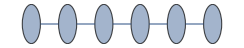

```mathematica
Graph[Range[0,qubitsnum-1],Table[j<->j+1,{j,0,qubitsnum-2}],VertexLabels->Placed[Automatic,Center],VertexSize->.5]
```

```mathematica
Options[ToyDevice]={
qubitsNum->qubitsnum,
(*average of T1*)
T1->10^5,
(* T2 *)
T2->10,
(* Set the standard depolarising and dephasing passive noise using T1 and T2/T2s *)
StdPassiveNoise->True,
(* Fidelities of X-, Y-, and Z- rotations by random benchmarking *)
FidSingle->0.995,
(* Error fraction/ratio {depolarising, dephasing} sum is either one or zero *)
EFSingle->{0,1},
(* Single qubit gate frequency *)
RabiFreq->10,
(* Fidelities of X-, Y-, and Z- rotations by random benchmarking *)
FidTwo->0.995,
(* Error fraction/ratio of two-qubit gates {depolarising, dephasing} which is is either one or zero *)
EFTwo->{0,1},
(* The frequency of driving qubit gates *)
TwoGateFreq->10
};
```

Native gates: Rx_j[θ],  Ry_j[θ], C_i[Z_(i+1)],Meas, Init,  Wait_-1[Δt]

## Compilation : QFT

```mathematica
QFT[nqubit_,swap_:False]:=Flatten@Join[{If[swap,Table[Subscript[SWAP, i,nqubit-i-1],{i,0,IntegerPart[nqubit/2]-1}],{}],{Subscript[H, 0]}},Table[Join[Table[Subscript[C, m][Subscript[Ph, i][π 2^(-m-1)]],{m,0,i-1}],{Subscript[H, i]}],{i,1,nqubit-1}]]
```

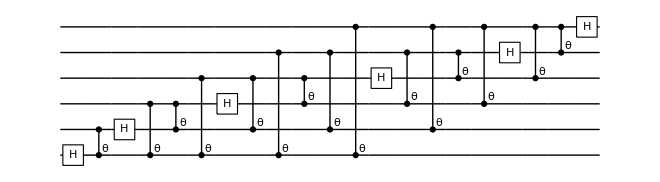

```mathematica
DrawCircuit[QFT[qubitsnum]]
```

```mathematica
unitary=CalcCircuitMatrix@QFT@qubitsnum;
dev=ToyDevice[];
```

```mathematica
DestroyAllQuregs[];
conf=DefaultConfig[dev,unitary,10];
```

```mathematica
conf["fixansatz"]={Subscript[Rx, 0][θ],Subscript[Rz, 0][θ],Subscript[C, 0][Subscript[Rz, 1][θ]],Subscript[Rz, 0][θ],Subscript[C, 0][Subscript[Rz, 1][θ]],Subscript[Rz, 1][θ]};
conf["grad"]="NG";
```

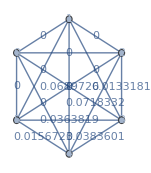

```mathematica
g=QMIGraph[0,qubitsnum]
```

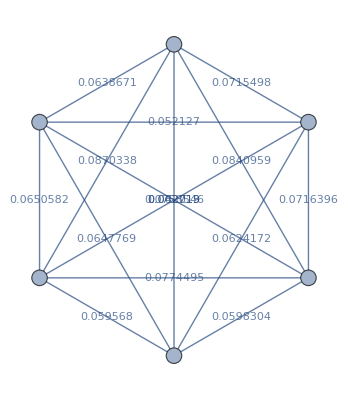

```mathematica
g=QMIGraphAvg[QMIGraph[#,qubitsnum]&/@{0,1,2,3,4,5}]
```

```mathematica
?probZeros
```

```mathematica
p=probZeros[qubitsnum,{0,1,2,3,4,5}]
```

<|0→0.158836,1→0.1456,2→0.198213,3→0.140012,4→0.197965,5→0.159374|>

```mathematica
singleRGate[conf,p]
```

Ry_1[θ]

```mathematica
Clear[g]
```

```mathematica
twoRGate[conf,g]
```

{C_2[Ry_3[θ]],C_3[Rz_4[θ]],C_4[Rz_5[θ]]}

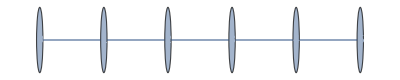

```mathematica
conf["connectivity"]
```

```mathematica
conf["grad"]="SGD";
```

Compilation with a fixed ansatz

{0<->1→0.520419,0<->2→0.082877,1<->2→0.317194}

-Graphics-

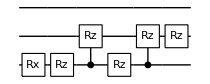
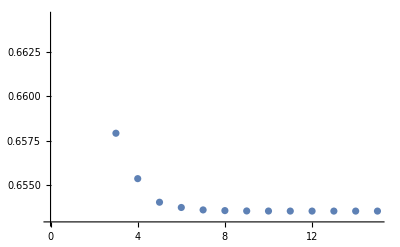
0.65354
-Graphics-
{Rx_0[θ_1],Rz_0[θ_2],C_0[Rz_1[θ_3]],Rz_0[θ_4],C_0[Rz_1[θ_5]],Rz_1[θ_6]}
<|θ_1→1.51914,θ_2→0.697711,θ_3→0.566609,θ_4→0.697712,θ_5→0.566608,θ_6→2.18731|>
-Graphics-

{0.636715,0.65354}

```mathematica
Timing[CircuitSynthesis[3,conf]//First]
```